### lib

Specify path to project:

```mathematica
ProjectPath = "/Users/sunfun/projects/shipit";
shipitCmd = ProjectPath <> "/shipit";
```

```mathematica
SetOptions[{Plot, ListPlot,RegionPlot},GridLines->Automatic];
```

```mathematica
ToV[x_]:=x//Normal//Values;
```

```mathematica
GIndex[mean_,σ_,ksi_]:=ksi/σ^2+(ⅇ^(-mean^2/(2 σ^2)) σ)/(√(2 π))+1/2 mean (1+Erf[mean/(√2 σ)]);
MossIndex[mean_,σ_, s_,l_,psi_]:=(mean+s*σ*Sqrt[Max[psi,l+Log[σ]]]);

PIndex[mean_,σ_, s_]:=mean + s *σ;
```

```mathematica
ResultVsError[data_, mean_, sigma_, methods_]:=Module[
{prefilteredData, method},
prefilteredData=data[Select[ #["sigma"]==sigma && #["mean"]==mean& ]]//Sort;
(
method = #;
prefilteredData[Select[(#["m"]==method)& ], {"error", "result"}]//Sort
)&/@methods
]
```

```mathematica
AvgMeasurements[measurements_]:=Module[
{v,e, sumvw, sumw},
{sumvw, sumw}=Plus@@((
{v,e} = #;
{v/e^2, 1/e^2}
)&/@measurements);
{sumvw/sumw, Sqrt[1/sumw]}
];
```

```mathematica
NormalA[x_]:=Normal[x/.{a_±b_:> a}] /;! FreeQ[x, a_±b_]; 
SetAttributes[NormalA, {Listable}];
```

```mathematica
Round6[x_]:= Round[x,10.0^-6];
SetAttributes[Round6, {Listable}];
```

```mathematica
Clear[Shipit];
```

```mathematica
SetSharedFunction[ShipitM];

Shipit0[args__]:=Module[
{input, result, paramsRound},
input = ((ToString[#]<>" ")&/@Flatten[{args}] )// StringJoin;
result = RunProcess[shipitCmd, All,  input];
ImportString[result["StandardOutput"],"CSV"]//Flatten
];
(* point__ = (m_,seed_, weeks_,trials_,mean_, sigma_,error_) *)
Shipit[point__, params_]:= Module[
{input, result, paramsRound, memKey},
paramsRound=Round6[params];
memKey = ToString[{point, paramsRound}];
result=ShipitM[memKey];
If[
result =!= Null && Head[result]=!=ShipitM , 
result, 
result = Shipit0[point, paramsRound];
ShipitM[memKey]= result;
result
]
]
```

```mathematica
palette1= ColorData["Rainbow"][#]&/@Range[0.1,1,0.2]
palette2= ColorData["GreenPinkTones"][#]&/@Range[0.1,1,0.11]
```

{RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.8929546, 0.38966159999999994, 0.1794008]}

{RGBColor[0.0040354945, 0.568068, 0.0569705],RGBColor[0.09983128500000002, 0.87799845, 0.15298735000000002],RGBColor[0.4229240000000001, 0.967009, 0.4300436000000001],RGBColor[0.7761015000000001, 0.96462, 0.7750478000000001],RGBColor[0.9733956, 0.8343598999999999, 0.9720344000000001],RGBColor[0.9947572499999999, 0.5233977499999999, 0.99041525],RGBColor[0.9295473999999999, 0.26290779999999997, 0.926568],RGBColor[0.6712855500000001, 0.14407742000000004, 0.6713075500000002],RGBColor[0.3077854000000001, 0.06492684000000001, 0.30532590000000004]}

### Save and load ShipitM

```mathematica
<< (ProjectPath <> "/mem_shipit.nb");
```

```mathematica
Save[ProjectPath<>"/mem_shipit_new.nb", ShipitM];
```

### Test “shipit” binary

```mathematica
Shipit0[11, 1, 300000, 25, -1, 1, 16,{0.42, 1.0}]
```

{0.0846109,0.00220291}

```mathematica
Shipit0[30, 1, 300000, 25, -1, 1, 16,{ 1.9738814126886406, 0.5347630010785354, 0.01108}]
```

{0.107819,0.00247965}

```mathematica
Shipit0[32, 1, 300000, 25, -0.1, 1, 16,{0.4316821622352789, 1.0119072802518363}]
```

{1.77648,0.0256443}

```mathematica
Shipit0[14, 1, 300000, 25, -0.1, 1, 16,{1.6171875000000004, 0.0}]
```

{1.75609,0.0211305}

```mathematica
Shipit0[15, 1, 300000, 25, -0.1, 1, 16,{1.6171875000000004}]
```

{1.75609,0.0211305}

```mathematica
Shipit0[20, 1, 300000, 25, -1, 1, 16,{0.5929603648059317,Log[0.5929603648059317] + 11.85168706794350, 2, 1.82082485716244320}]
```

{0.109744,0.00273227}

```mathematica
Shipit0[21, 1, 300000, 25, -1, 1, 16,{0.5929603648059317,11, 1.82082485716244320}]
```

{0.109757,0.00260477}

### Compare m=14 vs m = 30 for mean=-0.5; sigma=1.0;

```mathematica
meanB0=-0.5;sigmaB0=1.0;
```

```mathematica
n=300000;
```

```mathematica
Shipit[30, 1, n, 25, meanB0, sigmaB0, 32,{0.96849, 0.64, -0.023}]
```

{0.361523,0.0103347}

```mathematica
Shipit[30, 1, n, 25, meanB0, sigmaB0, 32,{0.96849, 0.64, 0}]
```

{0.36149,0.0113858}

```mathematica
Shipit[30, 1,n, 25, meanB0, sigmaB0, 32,{1.28, 0.5, -0.023}]
```

{0.364108,0.0115462}

```mathematica
Shipit[30, 1, n, 25, meanB0, sigmaB0, 32,{1.352, 0.5, -0.013}]
```

{0.360436,0.0103673}

```mathematica
Shipit[14, 1, n, 25, meanB0, sigmaB0, 32,{1.43, 0.0}]
```

{0.357934,0.0099414}

```mathematica
sp0=1.419913;
```

```mathematica
sg0=1.352;ksig0=0.0;
```

```mathematica
(* sm0=0.64;l0=20.0; ksim0=2.27; *)
```

```mathematica
sm0=0.646;l0=3.82; ksim0=3.62;
```

```mathematica
Manipulate[
RegionPlot[
{
PIndex[mean,sigma,sp]< PIndex[meanB,sigmaB,sp],
GIndex[mean,sg*sigma,ksig]< GIndex[meanB,sg*sigmaB,ksig],
MossIndex[mean, sigma,sm,l,ksi]< MossIndex[meanB,sigmaB,sm,l,ksi]
},
{mean, -0.6,0.1},
{sigma, 0.4,1.2}
],
{{meanB, meanB0}, -2,0},
{{sigmaB, sigmaB0}, 0.1,2},
{{sg, sg0}, 0.2,2.2},
{{ksig, ksig0}, -0.1,0.1},
{{sp, sp0}, 0.2,2.2},
{{sm, sm0}, 0.2,2.2},
{{l, l0}, 0.1,24},
{{ksim, ksim0}, -0.5,15.0}
]
```

```mathematica
sigma0 = PIndex[meanB0, sigmaB0, sp0]/sp0
```

0.647866

```mathematica
ksi = 3.82 + Log[(sigmaB0+sigma0)/2]
```

3.62633

```mathematica
meanCnd[mean_]:=(#["mean"]==mean&);
```

```mathematica
MemberQ[{1,2,3},1]
```

True

```mathematica
Unprotect[Element];
x_ ∈ s_List:=MemberQ[s,x]
Protect[Element];
```

### Import shipit_results.txt

```mathematica
file="~/projects/shipit/shipit_results.txt";
```

```mathematica
fields=StringSplit[
"result\tresult_sigma\tm\tseed\tweeks\ttrials\tmean\tsigma\terror\tp1\tp2\tp3\tp4\tp5","\t"
];
intFields={"m", "seed", "weeks", "trials"};
types = Association[(#->"Number")&/@fields];
(types[#]="Integer";)&/@intFields;
types
```

<|result→Number,result_sigma→Number,m→Integer,seed→Integer,weeks→Integer,trials→Integer,mean→Number,sigma→Number,error→Number,p1→Number,p2→Number,p3→Number,p4→Number,p5→Number|>

```mathematica
data0=SemanticImport[file, types]
```

Dataset[<>]

```mathematica
data1=data0[Select[#["m"]!=11&]];
```

```mathematica
KeyFn[r_]:=HK[r["m"],r["mean"],r["sigma"],r["error"]];
dataHash=<||>;
(
r=#;
k=KeyFn[r];
If[
Lookup[dataHash, k,Null]==Null || 
dataHash[k]["weeks"]<r["result"]||
dataHash[k]["result"]<r["result"],
dataHash[k]=r
];
)&/@data1[Select[#["weeks"]≥1000000&]];

data=(Dataset[Values[dataHash]]//Sort );
```

```mathematica
{Length[data0],Length[dataHash]}
```

{1295,1142}

```mathematica
prefilteredData=data[Select[ #["sigma"]==1 && #["mean"]==-1& ]]//Sort;
```

```mathematica
prefilteredData[Select[( #["error"]==35) & ]]//Sort
```

```mathematica
prefilteredData[Select[(#["m"]==14)& ]]
```

```mathematica
d10=prefilteredData[Select[(#["m"]==10)& ]]//Sort;
d12=prefilteredData[Select[(#["m"]==12)& ]]//Sort;
d14=prefilteredData[Select[(#["m"]==14)& ]]//Sort;
d20=prefilteredData[Select[(#["m"]==20)& ]]//Sort;
d21=prefilteredData[Select[(#["m"]==20)& ]]//Sort;
d30=prefilteredData[Select[( #["m"]==30)& ]]//Sort;
d32=prefilteredData[Select[( #["m"]==32)& ]]//Sort;
```

```mathematica
basicMs={14,20,30,32};
```

### mean = -1, sigma = 1. Plot result vs error

```mathematica
d14
```

```mathematica
d21
```

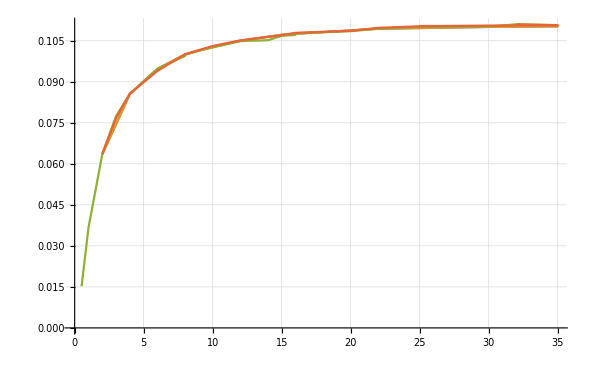

```mathematica
ListPlot[
{
d12[All, {"error", "result"}],
d14[All, {"error", "result"}],
d21[All, {"error", "result"}]//Sort,
d30[All, {"error", "result"}]
},
Joined->True]
```

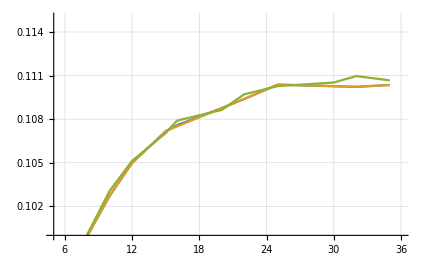

```mathematica
ListPlot[
{
d12[All, {"error", "result"}]//Sort,
d14[All, {"error", "result"}]//Sort,
d30[All, {"error", "result"}]//Sort
},
Joined->True,PlotRange->{{5,36},{0.10,0.115}}
]
```

```mathematica
dss=ResultVsError[data, -1, 1, basicMs]
```

{,,,}

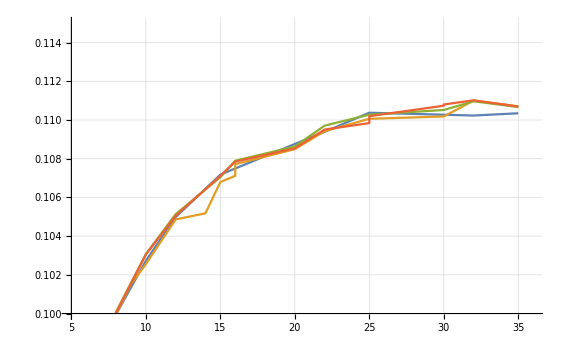

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.10,0.115}}
]
```

### mean = -0.5, sigma = 1. Plot result vs error

```mathematica
dss=ResultVsError[data, -0.5, 1, basicMs];
```

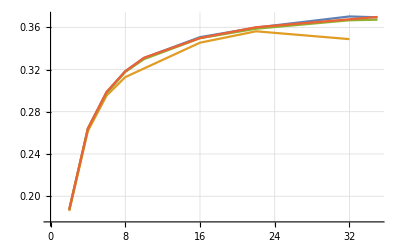

```mathematica
ListPlot[dss,Joined->True]
```

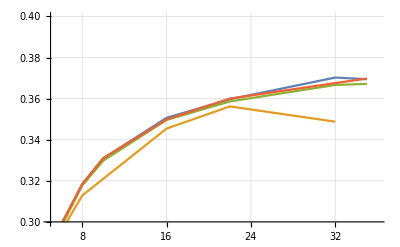

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.30,0.4}}
]
```

### mean = -1.5, sigma = 1. Plot result vs error

```mathematica
dss=ResultVsError[data, -1.5, 1, basicMs];
```

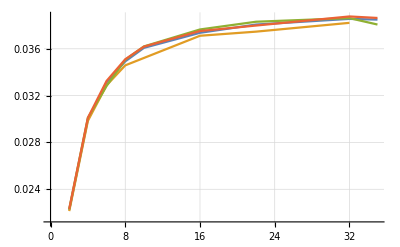

```mathematica
ListPlot[dss,Joined->True]
```

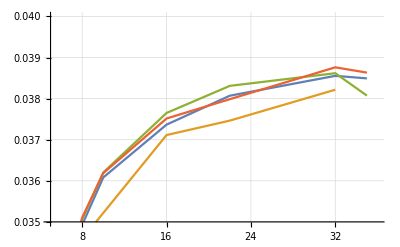

```mathematica
ListPlot[
dss,
Joined->True,PlotRange->{{5,36},{0.035,0.040}}
]
```

### Region plots for all methods

#### GIndex, m = 30

```mathematica
Off[General::munfl]
```

```mathematica
d30[Select[#["mean"]==-1&&#["error"]==16 &],All]
```

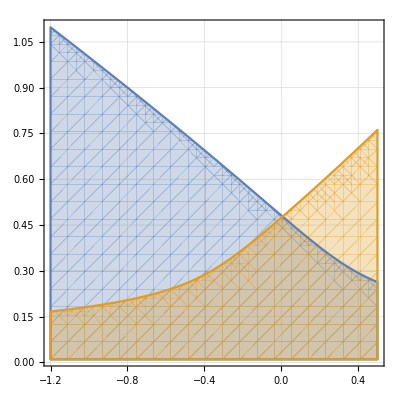

```mathematica
meanB=-1.0;sigmaB=1.0;  
ship=0.97559; s=0.8029; ksi=-0.022;
g7=RegionPlot[
{
GIndex[mean,s * sigma,ksi] <=  GIndex[meanB,s * sigmaB,ksi],
GIndex[mean,s * sigma,ksi] *ship <= mean
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

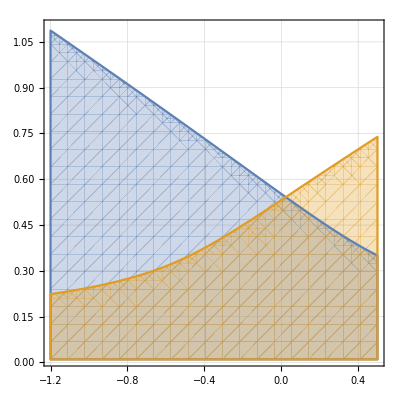

```mathematica
meanB=-1.0;sigmaB=1.0;  
ship=1.0; s=1.0; ksi=-0.06;
g30=RegionPlot[
{
GIndex[mean,s * sigma,ksi] <=  GIndex[meanB,s * sigmaB,ksi],
GIndex[mean,s * sigma,ksi] *ship <= mean
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

#### PValue, m = 12

```mathematica
d12[Select[#["mean"]==-1&&#["error"]==16 &],All]
```

mean + lStop * σ < meanBase + lStop * σBase
mean > (sigma-sigma0)*lShip

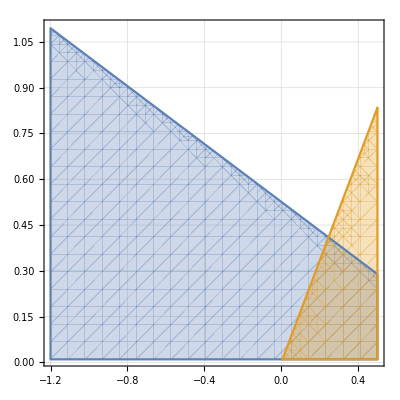

```mathematica
meanB=-1.0;sigmaB=1.0;  
 lShip=0.599; lStop=2.11; sigma0=0.0;
g12=RegionPlot[
{
PIndex[mean,sigma,lStop] <=  PIndex[meanB,sigmaB,lStop],
PIndex[-mean,sigma-sigma0,lShip]  <= PIndex[0,sigma0,ksi]
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

#### PValue, m = 14

```mathematica
d14[Select[#["mean"]==-1&&#["error"]==15 &],All]
```

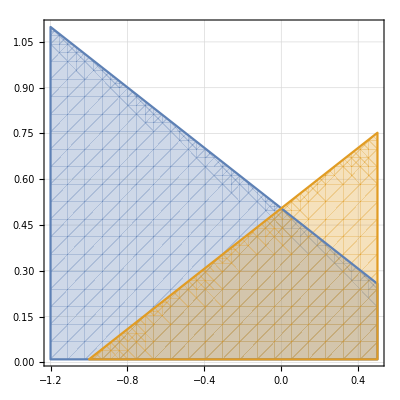

```mathematica
meanB=-1.0;sigmaB=1.0;  
 lStop=2.02;  lShip=lStop + 0.0000608;
 sigma0=PIndex[meanB, sigmaB, lStop]/lStop;
g14=RegionPlot[
{
PIndex[mean,sigma,lStop] <=  PIndex[meanB,sigmaB,lStop],
PIndex[-mean,sigma,lShip] <= PIndex[0,sigma0,lShip]
},
{mean, -1.2,0.5},
{sigma, 0.01,1.1}
]
```

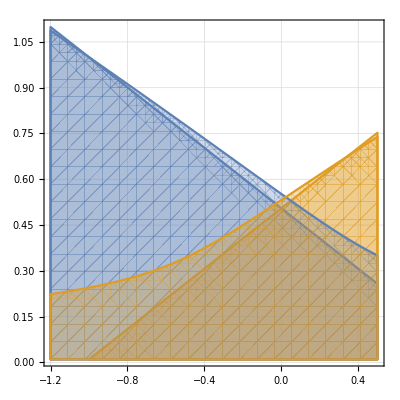

```mathematica
Show[{g14, g30}]
```

### Define DataRegions to draw regions from data

```mathematica
DataRegions[data_, cnds_, rCndsFn_]:=Module[
{filteredData, r},
filteredData=data[Select[cnds[#]&& #["mean"]<0& ]]//Sort;
(
(
r=#;
{rCndsFn[r["mean"], r["sigma"], {r["p1"], r["p2"], r["p3"],r["p4"],r["p5"]}],r}
)&/@filteredData
) // Normal//Transpose
]
```

### m = 12 DataRegions

```mathematica
(* p-value *)
RCndsM11[baseMean_, baseSigma_,{pShipSigmas_,pStopSigmas_,others___}]:=(
PIndex[mean,sigma,pStopSigmas] <=  0 ||
PIndex[-mean,sigma,pShipSigmas] <= 0
);
```

```mathematica
RCndsM12[baseMean_, baseSigma_,{pShipSigmas_,pStopSigmas_,sigmaMul_,others___}]:=(
PIndex[mean,sigma,pStopSigmas] <=  PIndex[baseMean,baseSigma,pStopSigmas] ||
PIndex[-mean,sigma,pShipSigmas] <= PIndex[0,sigmaMul * baseSigma,pShipSigmas]
);
```

```mathematica
{regs12, rs12}=DataRegions[data, #["m"]==12&&#["error"]==32&, RCndsM12];
```

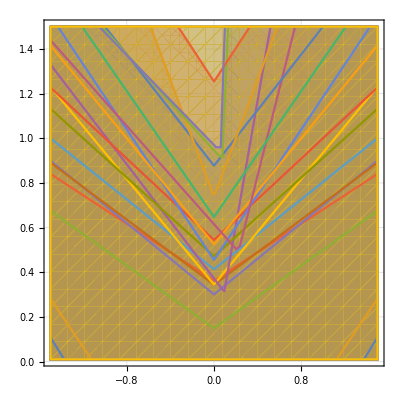

```mathematica
RegionPlot[
Evaluate[regs12//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}
]
```

### m = 14, 13 DataRegions

```mathematica
RCndsM13[baseMean_, baseSigma_,{pShipSigmas_, pStopSigmas_,others___}]:=Module[
{sigmaMul},
 sigmaMul=PIndex[baseMean, baseSigma, pStopSigmas]/pStopSigmas/ baseSigma;
RCndsM12[baseMean, baseSigma,{pShipSigmas, pStopSigmas,sigmaMul}]
];
```

```mathematica
RCndsM14[baseMean_, baseSigma_,{pStopSigmas_, pA_,others___}]:=Module[
{sigmaMul, pShipSigmas},
pShipSigmas = pStopSigmas + pA;
 sigmaMul=PIndex[baseMean, baseSigma, pStopSigmas]/pStopSigmas/ baseSigma;
RCndsM12[baseMean, baseSigma,{pShipSigmas, pStopSigmas,sigmaMul}]
];
```

```mathematica
{regs14, rs14}=DataRegions[data, #["m"]==14 && #["error"]==32&, RCndsM14];
```

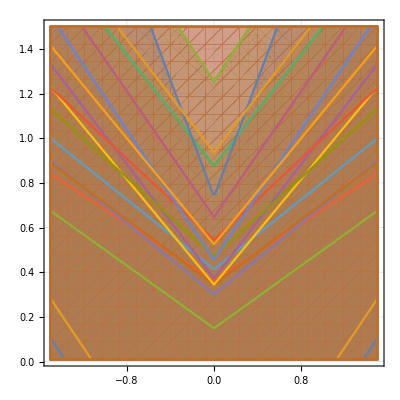

```mathematica
RegionPlot[
Evaluate[regs14//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}
]
```

### m = 30 DataRegions

```mathematica
RCndsM30[baseMean_,baseSigma_,{pS_, pShip_, pKsi_, other___}]:=(
GIndex[mean,pS * sigma,pKsi] <=  GIndex[baseMean,pS * baseSigma,pKsi]||
GIndex[mean,pS * sigma,pKsi] *pShip <= mean
);
```

```mathematica
{regs30, rs30}=DataRegions[data, #["m"]==30 && #["error"]==32&, RCndsM30];
```

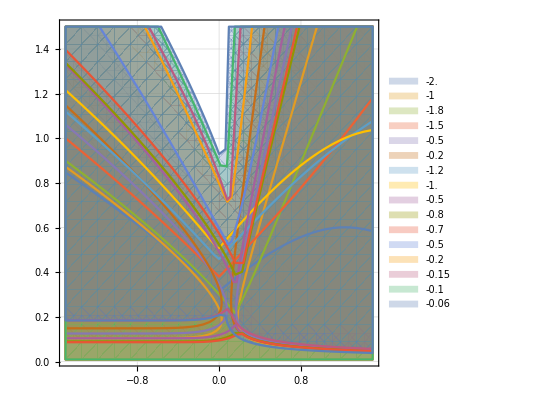

```mathematica
RegionPlot[
Evaluate[regs30//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}, PlotLegends->(#["mean"]&)/@rs30
]
```

```mathematica
{regs30, rs30}=RegionsM30[data, #["sigma"]==1&& #["mean"]==-1&& #["error"]∈{16,32,35}&];
```

Set::shape: Lists {regs30,rs30} and RegionsM30[Dataset[«1142»],#1[sigma]==1&&#1[mean]==-1&&#1[error]∈{16,32,35}&] are not the same shape.

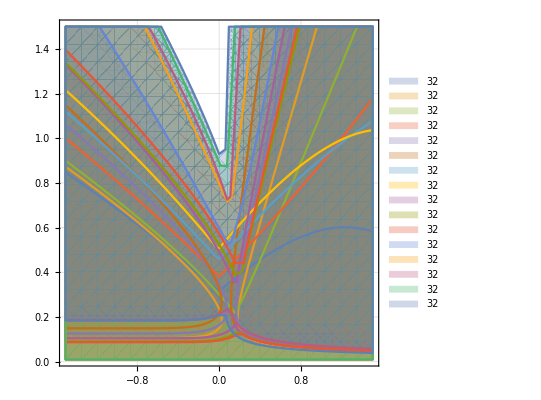

```mathematica
RegionPlot[
Evaluate[regs30//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}, PlotLegends->(#["error"]&)/@rs30
]
```

### m = 32 DataRegions

```mathematica
RCndsM32[baseMean_, baseSigma_, {pS_, pShip_,other___}]:=Module[
{pKsi}, 
pKsi=-(baseSigma*pS)^2*GIndex[baseMean,pS * baseSigma,0];
 RCndsM30[baseMean, baseSigma, {pS, pShip, pKsi}] 
]
```

```mathematica
data[Select[ #["error"]==35 && #["m"]==32&& #["mean"]<0& ]]//Sort
```

```mathematica
{regs32, rs32}=RegionsM32[data, #["error"]==35&];
```

Set::shape: Lists {regs32,rs32} and RegionsM32[Dataset[«1142»],#1[error]==35&] are not the same shape.

```mathematica
RegionPlot[
Evaluate[regs32//Normal],
{mean, -1.5, 1.5},
{sigma, 0.01, 1.5}, PlotLegends->(#["mean"]&)/@rs32
]
```

-Graphics-

### Ship-it for params : m = 14, sigma = 1, mean = –1, error = 16

```mathematica
d14
```

Shipit[m_, seed_, weeks_, trials_, mean_, sigma_, error_, params_]

```mathematica
shFn[p_,a_]:=Shipit[14,1,10000000, 25, -1,1,16, {p, a}][[1]];
```

```mathematica
range=Range[1.6,2.5,0.1];
l1=ParallelMap[{#,shFn[#,0]}&,range];
l2=ParallelMap[{#,shFn[#,-0.1]}&,range];
l3=ParallelMap[{#,shFn[#,0.1]}&,range];
```

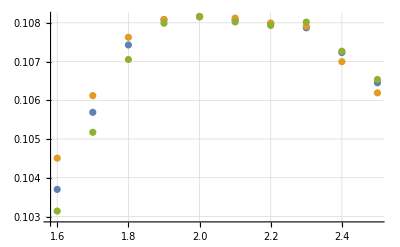

```mathematica
ListPlot[{l1,l2,l3}]
```

```mathematica
shM14E16N[p_,a_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[Shipit[14,#,10000000, 25, -1,1,16, {p, a}]&, Range[n]]];
```

```mathematica
range=Range[1.95,2.125,0.025]; 
n =50;
l1={#,shM14E16N[#,0,n]}&/@range;
l2={#,shM14E16N[#,0.1,n]}&/@range;
l3={#,shM14E16N[#,-0.1,n]}&/@range;
```

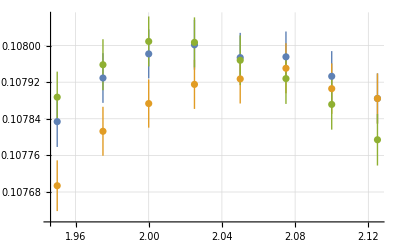

```mathematica
ListPlot[{l1,l2,l3}]
```

### Ship-it for params : m = 14, sigma = 1, mean = –1, error = 35

Shipit[m_, seed_, weeks_, trials_, mean_, sigma_, error_, params_]

```mathematica
shM14N[p_,a_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[Shipit[14,#,10000000, 25, -1,1,35, {p, a}]&, Range[n]]];
```

```mathematica
range = Range[2.0,2.15,0.025];
n=120;
l14n1={#,shM14N[#,0,n]}&/@range;
l14n2={#,shM14N[#,0.1,n]}&/@range;
l14n3={#,shM14N[#,-0.1,n]}&/@range;
```

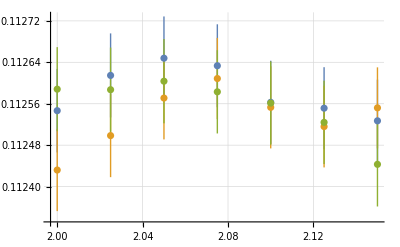

```mathematica
ListPlot[{l14n1,l14n2,l14n3}]
```

### Ship-it for params : m = 12, sigma = 1, mean = –1, error = 35

```mathematica
shM12N[stop_,a_,n_]:=Module[
{sigmaMul, baseMean, baseSigma},
baseMean = -1;
baseSigma=1;
sigmaMul=a(baseMean/baseSigma/stop + 1);
PlusMinus@@AvgMeasurements[ParallelMap[Shipit[12,#,10000000, 25, baseMean,baseSigma,35,{stop, stop, sigmaMul}]&, Range[n]]]
];
shM12N[stop_,ship_,a_,n_]:=Module[
{sigmaMul, baseMean, baseSigma},
baseMean = -1;
baseSigma=1;
sigmaMul=a(baseMean/baseSigma/stop + 1);
PlusMinus@@AvgMeasurements[ParallelMap[Shipit[12,#,10000000, 25, baseMean,baseSigma,35,{stop, ship, sigmaMul}]&, Range[n]]]
];
```

```mathematica
shM12N[2.05,1.0,50]
```

0.112624±0.000128659

```mathematica
shM12N[2.06,1.0,50]
```

0.112612±0.000129008

```mathematica
shM12N[2.07,0.98,50]
```

0.112599±0.00012669

```mathematica
shM12N[2.06,0.98,50]
```

0.112593±0.000126427

```mathematica
shM12N[2.05,0.98,50]
```

0.112619±0.000127159

```mathematica
shM12N[2.05,1.02,50]
```

0.112559±0.000130196

```mathematica
shM12N[2.0,2.05,0.97,50]
```

0.112468±0.000126235

### Ship-it for params : m = 30, sigma = 1, mean = –1, error = 35

Shipit[m_, seed_, weeks_, trials_, mean_, sigma_, error_, params_]

```mathematica
d30
```

```mathematica
shM30N[s_,ship_,ksi_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[Shipit[30,#,10000000, 25, -1,1,35, {s, ship,ksi}]&, Range[n]]];
```

```mathematica
range = Range[0.76,0.81,0.005];
n=50;
```

```mathematica
l1={#,shM30N[#,1.0,-0.02,n]}&/@range;
```

```mathematica
range = Range[0.62,0.67,0.005];
n=50;
```

```mathematica
l2={#+0.12,shM30N[#,1.0,-0.01,n]}&/@range;
```

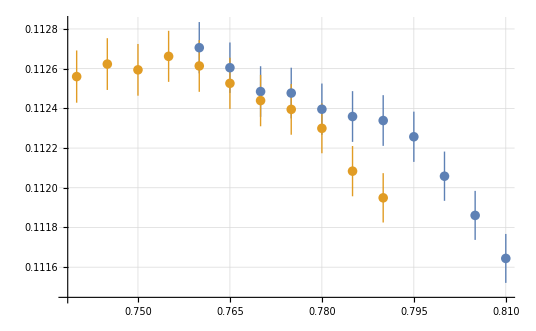

```mathematica
g30=ListPlot[{l1,l2}]
```

### Ship-it for params : m = 32, sigma = 1, mean = –1, error = 35

Shipit[m_, seed_, weeks_, trials_, mean_, sigma_, error_, params_]

```mathematica
d32
```

```mathematica
shM32N[p_,a_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[Shipit[32,#,10000000, 25, -1,1,35, {p, a}]&, Range[n]]];
```

```mathematica
range = Range[0.77,0.83,0.01];
n=100;
l1={#,shM32N[#,1.0,n]}&/@range;
l2={#,shM32N[#,0.98,n]}&/@range;
l3={#,shM32N[#,1.02,n]}&/@range;
```

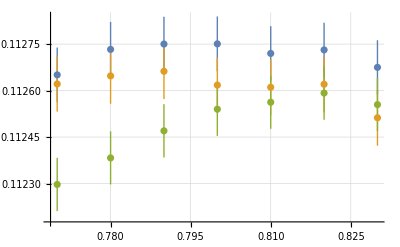

```mathematica
g32=ListPlot[{l1,l2,l3}]
```

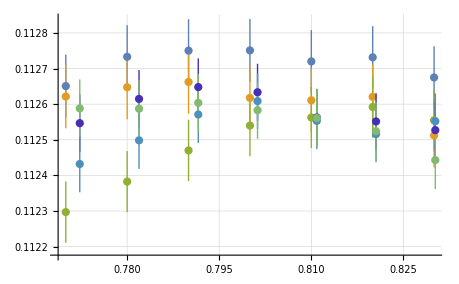

```mathematica
pr[l_]:={#[[1]]*0.78/2.02,#[[2]]}&/@l;
g14=ListPlot[Evaluate[pr/@{l14n1,l14n2,l14n3}], PlotStyle->palette1];
Show[g32, g14]
```

### Ship-it for params : m = 20, sigma = 1, mean = –1, error = 35

Shipit[m_, seed_, weeks_, trials_, mean_, sigma_, error_, params_]

```mathematica
d20
```

```mathematica
shM20[p_,l_,a_,b_,n_]:=Shipit[20,n,10000000, 25, -1,1,35, {p,l,a, b}];
shM20N[p_,a_,b_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[shM20[p,12.0,a,b, #]&, Range[n]]];
shM20N[p_,l_, a_,b_,n_]:=PlusMinus@@AvgMeasurements[ParallelMap[shM20[p,l,a,b,#]&, Range[n]]];
```

```mathematica
shM20[0.7,2.0,2.3, 1,1]
```

{0.00678657,0.000977172}

```mathematica
range = Range[0.55,0.61,0.01];
n=40;
l1={#,shM20N[#,2.0,2.3,n]}&/@range;
```

```mathematica
sm0=0.646;l0=3.82; ksim0=3.62;
```

```mathematica
n=40;
range = Range[0.98,1.02,0.01];
l2={#-0.4,shM20N[#,3.82, 2.0,3.62,n]}&/@range;
```

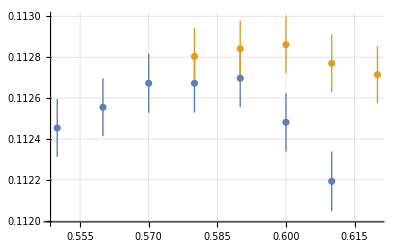

```mathematica
g20=ListPlot[{l1,l2}]
```

### Top mean = -1, sigma = 1, error = 35

```mathematica
data[Select[(#["mean"]==-1 && #["sigma"]==1 && #["error"]==35)&]] // Sort
```

```mathematica
n=700;
```

```mathematica
n=100;
```

```mathematica
r20=shM20N[1.0,3.82, 2.0,3.62,n]
```

0.112691±0.0000328508

```mathematica
r30=shM30N[0.795,1.0,-0.023,n]
```

0.112558±0.0000328412

```mathematica
r32=shM32N[0.795,1.0,n]
```

0.112656±0.0000330693

```mathematica
r14=shM14N[2.05,0,n]
```

0.112559±0.0000332555

```mathematica
r14a=shM14N[2.045,0,n]
```

0.112557±0.0000332291

```mathematica
r14b=shM14N[2.055,0,n]
```

0.112567±0.0000442064

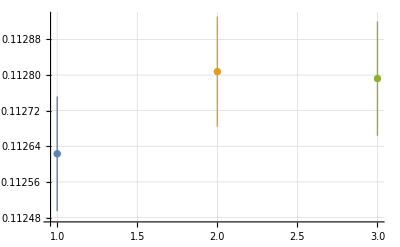

```mathematica
ListPlot[
{
{{1, r14}},
{{2, r20}},
{{3, r32}}
}
]
```

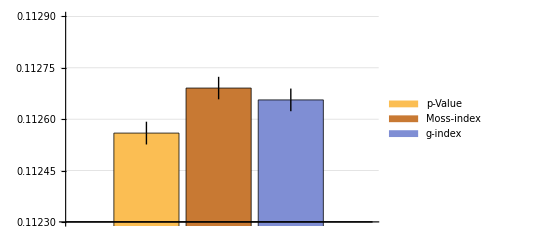

```mathematica
BarChart[
{
{r14,r20,r32}
}, 
ChartLegends->{"p-Value", "Moss-index", "g-index"},
PlotRange->{All, {0.1123, 0.1129}}, GridLines->Automatic
]
```